# Метод на най-малките квадрати (МНМК)

## Генериране на данни

```mathematica
xt = Table[-2+q*(0.13),{q,-10,1}]
```

{-3.3,-3.17,-3.04,-2.91,-2.78,-2.65,-2.52,-2.39,-2.26,-2.13,-2.,-1.87}

```mathematica
bigN = Length[xt]
```

12

```mathematica
f[x_]:=3*Sin[x-3]
yt = f[xt]
```

{-0.0504417,0.338831,0.722386,1.09375,1.44666,1.77515,2.07368,2.33722,2.56131,2.74218,2.87677,2.96282}

### Визуализация

#### графика на функцията (която НЕ знаем)

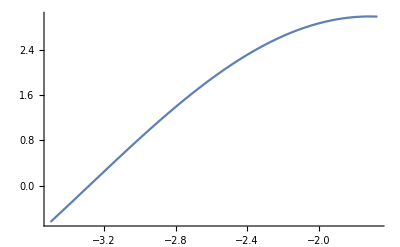

```mathematica
grf = Plot[f[x],{x,xt[[1]]-0.2,xt[[bigN]]+0.2}]
```

#### графика на точките (които знаем)

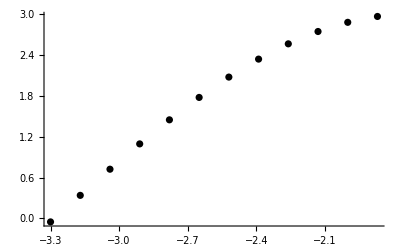

```mathematica
points = Table[{xt[[i]],yt[[i]]},{i,1,bigN}];
grp = ListPlot[points, PlotStyle->Black]
```

#### двете графики на едно

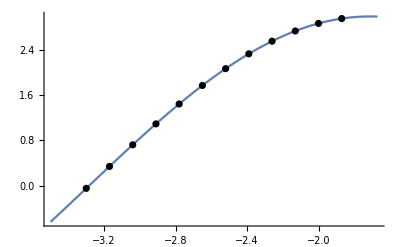

```mathematica
Show[grf,grp]
```

## Линейна регресия

### За попълване на таблицата с междинните резултати

```mathematica
xt^2
```

{10.89,10.0489,9.2416,8.4681,7.7284,7.0225,6.3504,5.7121,5.1076,4.5369,4.,3.4969}

```mathematica
yt*xt
```

{0.166458,-1.0741,-2.19605,-3.18281,-4.0217,-4.70414,-5.22567,-5.58595,-5.78857,-5.84085,-5.75355,-5.54046}

#### Сумите

```mathematica
∑_(i=1)^bigN xt[[i]]
```

-31.02

```mathematica
∑_(i=1)^bigN yt[[i]]
```

20.8803

```mathematica
∑_(i=1)^bigN xt[[i]]^2
```

82.6034

```mathematica
∑_(i=1)^bigN yt[[i]]*xt[[i]]
```

-48.7474

### Решаваме СЛАУ

```mathematica
A = ({{12, -31.02}, {-31.02, 82.6034}}); b = {20.8803, -48.7474};
LinearSolve[A,b]
```

{7.33229,2.16335}

### Съставяме полинома

```mathematica
P1[x_]:=2.16335 x + 7.33229
```

#### Визуализация

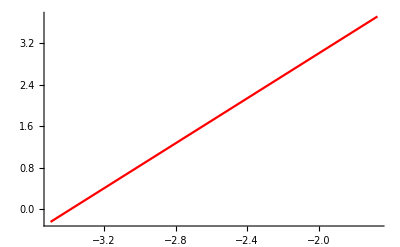

```mathematica
grP1 =Plot[P1[x],{x,xt[[1]]-0.2,xt[[bigN]]+0.2}, PlotStyle->Red]
```

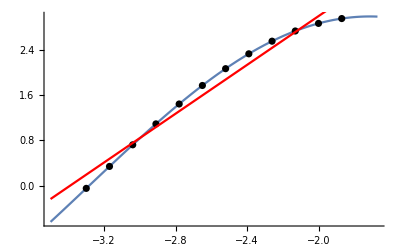

```mathematica
Show[grf,grp, grP1]
```

### Пресмятаме приближена стойност на функцията

```mathematica
P1[-2.5]
```

1.92392

### Оценка на грешката

#### Истинска грешка (за сравнение)

```mathematica
Abs[P1[-2.5]-f[-2.5]]
```

0.192706

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^bigN (yt[[i]]-P1[xt[[i]]])^2)
```

0.577383

## Квадратична регресия

### За попълване на таблицата с междинните резултати

```mathematica
xt^2
```

{10.89,10.0489,9.2416,8.4681,7.7284,7.0225,6.3504,5.7121,5.1076,4.5369,4.,3.4969}

```mathematica
yt*xt
```

{0.166458,-1.0741,-2.19605,-3.18281,-4.0217,-4.70414,-5.22567,-5.58595,-5.78857,-5.84085,-5.75355,-5.54046}

```mathematica
xt^3
```

{-35.937,-31.855,-28.0945,-24.6422,-21.485,-18.6096,-16.003,-13.6519,-11.5432,-9.6636,-8.,-6.5392}

```mathematica
xt^4
```

{118.592,100.98,85.4072,71.7087,59.7282,49.3155,40.3276,32.6281,26.0876,20.5835,16.,12.2283}

```mathematica
yt*xt^2
```

{-0.54931,3.40488,6.67601,9.26198,11.1803,12.466,13.1687,13.3504,13.0822,12.441,11.5071,10.3607}

#### Сумите

```mathematica
∑_(i=1)^bigN xt[[i]]
```

-31.02

```mathematica
∑_(i=1)^bigN yt[[i]]
```

20.8803

```mathematica
∑_(i=1)^bigN xt[[i]]^2
```

82.6034

```mathematica
∑_(i=1)^bigN yt[[i]]*xt[[i]]
```

-48.7474

```mathematica
∑_(i=1)^bigN xt[[i]]^3
```

-226.024

```mathematica
∑_(i=1)^bigN xt[[i]]^4
```

633.587

```mathematica
∑_(i=1)^bigN yt[[i]]*xt[[i]]^2
```

116.35

### Решаваме СЛАУ

```mathematica
A = ({{12, -31.02, 82.6034}, {-31.02, 82.6034, -226.02}, {82.6034, -226.02, 633.58}}); b = {20.8803, -48.7474, 116.35};
LinearSolve[A,b]
```

{1.71917,-2.31602,-0.866702}

```mathematica
Fit[points,{1,x,x^2},x]
```

1.34238-2.61503 x-0.924255 x^2

точно въвеждане с изразите:

```mathematica
A = ({{bigN, ∑_(i=1)^bigN xt[[i]], ∑_(i=1)^bigN xt[[i]]^2}, {∑_(i=1)^bigN xt[[i]], ∑_(i=1)^bigN xt[[i]]^2, ∑_(i=1)^bigN xt[[i]]^3}, {∑_(i=1)^bigN xt[[i]]^2, ∑_(i=1)^bigN xt[[i]]^3, ∑_(i=1)^bigN xt[[i]]^4}}); b = {∑_(i=1)^bigN yt[[i]], ∑_(i=1)^bigN yt[[i]]*xt[[i]], ∑_(i=1)^bigN yt[[i]]*xt[[i]]^2};
LinearSolve[A,b]
```

{1.34238,-2.61503,-0.924255}

### Съставяме полинома

```mathematica
P2[x_]:=-0.8667 x^2- 2.31602 x + 1.7191
```

#### Визуализация

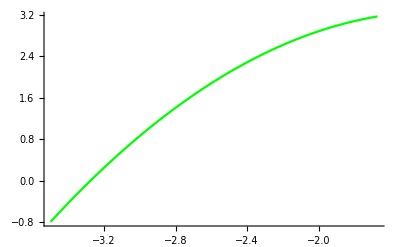

```mathematica
grP2 =Plot[P2[x],{x,xt[[1]]-0.2,xt[[bigN]]+0.2}, PlotStyle->Green]
```

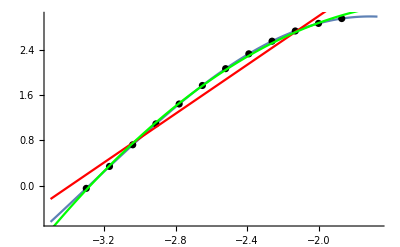

```mathematica
Show[grf,grp, grP1,grP2]
```

### Пресмятаме приближена стойност на функцията

```mathematica
P2[-2.5]
```

2.09228

за сравнение истинската стойност е

```mathematica
f[-2.5]
```

2.11662

### Оценка на грешката

#### Истинска грешка (за сравнение)

```mathematica
Abs[P2[-2.5]-f[-2.5]]
```

0.024346

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^bigN (yt[[i]]-P2[xt[[i]]])^2)
```

0.0948914

## Кубична регресия

### За попълване на таблицата с междинните резултати

```mathematica
xt^2
```

{10.89,10.0489,9.2416,8.4681,7.7284,7.0225,6.3504,5.7121,5.1076,4.5369,4.,3.4969}

```mathematica
yt*xt
```

{0.166458,-1.0741,-2.19605,-3.18281,-4.0217,-4.70414,-5.22567,-5.58595,-5.78857,-5.84085,-5.75355,-5.54046}

```mathematica
xt^3
```

{-35.937,-31.855,-28.0945,-24.6422,-21.485,-18.6096,-16.003,-13.6519,-11.5432,-9.6636,-8.,-6.5392}

```mathematica
xt^4
```

{118.592,100.98,85.4072,71.7087,59.7282,49.3155,40.3276,32.6281,26.0876,20.5835,16.,12.2283}

```mathematica
yt*xt^2
```

{-0.54931,3.40488,6.67601,9.26198,11.1803,12.466,13.1687,13.3504,13.0822,12.441,11.5071,10.3607}

```mathematica
xt^5
```

{-391.354,-320.108,-259.638,-208.672,-166.044,-130.686,-101.626,-77.9811,-58.9579,-43.8428,-32.,-22.8669}

```mathematica
xt^6
```

{1291.47,1014.74,789.299,607.237,461.603,346.318,256.096,186.375,133.245,93.3851,64.,42.7612}

```mathematica
yt*xt^3
```

{1.81272,-10.7935,-20.2951,-26.9524,-31.0813,-33.0348,-33.1851,-31.9075,-29.5657,-26.4993,-23.0142,-19.3745}

#### Сумите

```mathematica
∑_(i=1)^bigN xt[[i]]
```

-31.02

```mathematica
∑_(i=1)^bigN yt[[i]]
```

20.8803

```mathematica
∑_(i=1)^bigN xt[[i]]^2
```

82.6034

```mathematica
∑_(i=1)^bigN yt[[i]]*xt[[i]]
```

-48.7474

```mathematica
∑_(i=1)^bigN xt[[i]]^3
```

-226.024

```mathematica
∑_(i=1)^bigN xt[[i]]^4
```

633.587

```mathematica
∑_(i=1)^bigN yt[[i]]*xt[[i]]^2
```

116.35

```mathematica
∑_(i=1)^bigN xt[[i]]^5
```

-1813.78

```mathematica
∑_(i=1)^bigN xt[[i]]^6
```

5286.53

```mathematica
∑_(i=1)^bigN yt[[i]]*xt[[i]]^3
```

-283.891

### Решаваме СЛАУ

```mathematica
A = ({{bigN, ∑_(i=1)^bigN xt[[i]], ∑_(i=1)^bigN xt[[i]]^2, ∑_(i=1)^bigN xt[[i]]^3}, {∑_(i=1)^bigN xt[[i]], ∑_(i=1)^bigN xt[[i]]^2, ∑_(i=1)^bigN xt[[i]]^3, ∑_(i=1)^bigN xt[[i]]^4}, {∑_(i=1)^bigN xt[[i]]^2, ∑_(i=1)^bigN xt[[i]]^3, ∑_(i=1)^bigN xt[[i]]^4, ∑_(i=1)^bigN xt[[i]]^5}, {∑_(i=1)^bigN xt[[i]]^3, ∑_(i=1)^bigN xt[[i]]^4, ∑_(i=1)^bigN xt[[i]]^5, ∑_(i=1)^bigN xt[[i]]^6}}); b = {∑_(i=1)^bigN yt[[i]], ∑_(i=1)^bigN yt[[i]]*xt[[i]], ∑_(i=1)^bigN yt[[i]]*xt[[i]]^2, ∑_(i=1)^bigN yt[[i]]*xt[[i]]^3};
a = LinearSolve[A,b]
```

{-4.71921,-9.91613,-3.80018,-0.370848}

за сравнение:

```mathematica
Fit[points,{1,x,x^2,x^3},x]
```

-4.71921-9.91613 x-3.80018 x^2-0.370848 x^3

### Съставяме полинома

```mathematica
P3[x_]:=a[[1]]+a[[2]]x+a[[3]] x^2+a[[4]] x^3
```

#### Визуализация

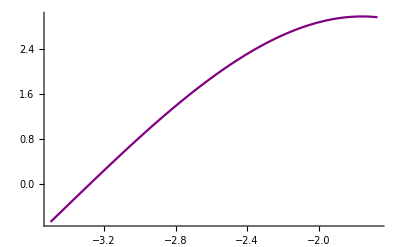

```mathematica
grP3 =Plot[P3[x],{x,xt[[1]]-0.2,xt[[bigN]]+0.2}, PlotStyle->Purple]
```

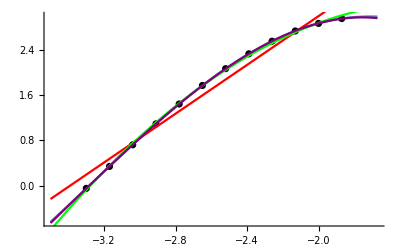

```mathematica
Show[grf,grp, grP1,grP2, grP3]
```

### Пресмятаме приближена стойност на функцията

```mathematica
P3[-2.5]
```

2.11446

за сравнение истинската стойност е

```mathematica
f[-2.5]
```

2.11662

### Оценка на грешката

#### Истинска грешка (за сравнение)

```mathematica
Abs[P3[-2.5]-f[-2.5]]
```

0.00215715

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^bigN (yt[[i]]-P3[xt[[i]]])^2)
```

0.00688749